```mathematica
SetDirectory[NotebookDirectory[]]
Get["eigenfaces-algorithm.m"]
{eigenvalues, eigenfaces}=findEigenfaces[normalizedFaces];
```

/home/nathan/QEA-Eigenfaces/Eigenfaces

```mathematica
components=Map[eigenCompress[#1,eigenfaces[[2;;3]],All]&,images];
components=Partition[components,8];
components=MapThread[Labeled[#1,#2]&,{components,names}];
```

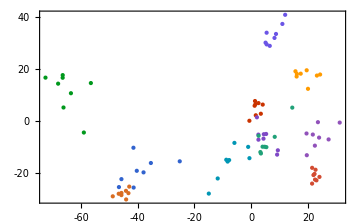

```mathematica
ListPlot[components[[9;;19]],PlotStyle->PointSize[Large],ImageSize->Medium,PlotTheme->"Web"]
```

```mathematica
components3=Map[eigenCompress[#1,eigenfaces[[40;;42]],All]&,images];
components3=Partition[components3,8];
(*components3=MapThread[Labeled[#1,#2]&,{components3,names}];*)
ListPointPlot3D[components3[[All]],PlotStyle->PointSize[Large],ImageSize->Large]
```

-Graphics3D-

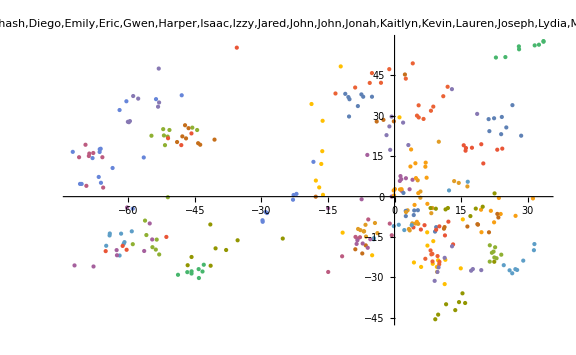

```mathematica
components=Map[eigenCompress[#1,eigenfaces[[2;;3]],All]&,images];
components=Partition[components,8];
ListPlot[components[[All]],PlotStyle->PointSize[Large],ImageSize->Large,PlotLabel->names]
```

```mathematica
MapThread[{#1,#2}&,{names,Range[Length@names]}]
```

{{Ariana,1},{Bryan,2},{Charlie,3},{Chloe,4},{Chris,5},{Danny,6},{David,7},{Dhash,8},{Diego,9},{Emily,10},{Eric,11},{Gwen,12},{Harper,13},{Isaac,14},{Izzy,15},{Jared,16},{John,17},{John,18},{Jonah,19},{Kaitlyn,20},{Kevin,21},{Lauren,22},{Joseph,23},{Lydia,24},{Margo,25},{Mark,26},{Mary,27},{Max,28},{Mica,29},{Nathan,30},{Paige,31},{Rebecca,32},{Regina,33},{Ruby,34},{Sam,35},{Sarah,36},{Sean,37},{Siddhartan,38},{Min,39},{Sung,40},{Taylor,41},{Uma,42},{Willem,43}}